```mathematica
a=Import["/Users/stevenschowalter/desktop/mms2-5.txt.txt","Data"];
```

```mathematica
b= Drop[a,2];
```

```mathematica
c= Flatten[Take[b,All,-1]];
```

```mathematica
{num}=Dimensions[c];
```

```mathematica
binnum=Table[0,{i,num}];
```

```mathematica
step=.1;
k=0;
x=1;
```

```mathematica
stoop=Table[0,{i,20/step}];
```

```mathematica
Do[
{
Do[
If[c[[i]]≥k*step&&c[[i]]<(k+1)*step,
{
x++;
}
],{i,1,2425}];
stoop[[k+1]]={k*step,x};
x=0;
}
,{k,0,20/step-1}
]
```

```mathematica
datpl=ListPlot[stoop,PlotRange->All];
```

```mathematica
fit=FindFit[Drop[stoop,8],aa ⅇ^(-bb t),{aa,bb},t]
```

{aa→101.276,bb→0.532897}

```mathematica
fitpl=Plot[aa ⅇ^(-bb t)/.fit,{t,0,20},PlotRange->All,PlotStyle->{Red,Thickness[.01]}];
```

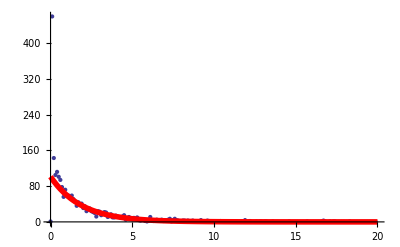

```mathematica
Show[datpl,fitpl]
```

```mathematica
(bb/.fit)^-1
```

1.87654